# Visualizing Normalization

## A graphical presentation of NMR normalization methods.

Eric Moyer

Started 27 May 2012

## Introduction

Normalization methods in NMR spectrography (and probably other spectrographic fields as well) are typically explained by the procedures that you go through to perform them and justified by arguments about the "real concentration." Another way to look at normalization methods is to examine them as geometric operations on a vector space. This gives a different understanding of what is occurring, which can give the practitioner a deeper intuition about trade-offs he makes when he says, "sum-normalize the data."

I look at each spectrum generated as a point in a vector space, one variable in the vector for each value measured. I am mainly concerned with frequency-domain spectra, since it is on these that the normalization methods I present are typically used. The normalization methods do not solve extant problems on time-domain spectra, so they are not used there. However, my points are just as valid for time-domain spectra, since they too are vectors.

## Sum Normalization

Sum normalization takes each spectrum, divides it by its sum, and then multiplies it by a constant. After this operation, all spectra have the same sum.

If the spectra are interpreted as points in an n-dimensional vector space, this projects all points onto (a set of) n-1 dimensional subspaces (hyperplanes) along a line between the original point and the origin. In 3 dimensions, it projects points onto 8 planes forming an octahedron about the origin. In 2 dimensions, all points are projected onto a square rotated  90-degrees. The size of these figures is determined by the constant.

How can we see this?

First, consider that multiplying a (non-zero) point by a constant moves it along a line connecting the point with the origin. Multiplying by a positive number less than 1 moves it closer to the origin. Multiplying by a number greater than 1 moves farther from the origin. And multiplying it by a negative number moves it away from the origin on the opposite side.

```mathematica
xPlusYEq1TwoD=Show[Plot[{1-x,x-1},{x,0,1},PlotStyle->Red],Plot[{x+1,-1-x},{x,-1,0},PlotStyle->Red],PlotRange->{-1,1}];
```

```mathematica
yEq2X=Plot[{2x},{x,0,3/2},PlotStyle->Darker[Blue]];
```

```mathematica
ptX3HalvesY3AndProjection=ListPlot[{{{3/2,3}},{{1/3,2/3}}},PlotMarkers->{Automatic,Medium},PlotStyle->{Darker[Blue],Darker[Magenta]}];
```

```mathematica
firstDiagram=Show[{xPlusYEq1TwoD,Graphics[{Text["Constant sum surface",{5/8,-1/2},{-1,0},BaseStyle->{Red}],Text["Spectrum",{3/2,11/4},{-1,0},BaseStyle->{Darker[Blue]}]}],yEq2X,ptX3HalvesY3AndProjection},PlotRange->All,AspectRatio->Automatic,ImageSize->{300},PlotRangeClipping->False];
```

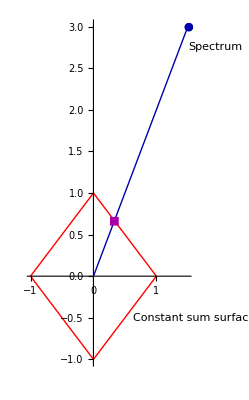
-Graphics-Figure 1: Sum Normalization in Two Dimensions

```mathematica
firstDiagramWithCaption=Labeled[firstDiagram,"Figure 1: Sum Normalization in Two Dimensions",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

The point at which the line through the origin intersects with the surface of points whose sum equals the target sum of the sum-normalization is the normalized point. Figures 1 and 2 show sum-normalization in two and three dimensions with a target sum of 1.

```mathematica
quarterOctahedron=Polygon[{{{0,0,1},{0,1,0},{1,0,0}},{{0,0,-1},{0,1,0},{1,0,0}}}];
```

```mathematica
sumEq1ThreeD=Graphics3D[{Opacity[0.85],Red,quarterOctahedron,Rotate[quarterOctahedron,Pi/2,{0,0,1}],Rotate[quarterOctahedron,Pi,{0,0,1}],Rotate[quarterOctahedron,3Pi/2,{0,0,1}]},Axes->True,Lighting->"Neutral"];
```

```mathematica
yEq2XThreeD=Graphics3D[{Darker[Blue],Line[{{0,0,0},{3/2,0,3}}],PointSize[Large],Point[{3/2,0,3}],Darker[Magenta],Point[{1/3,0,2/3}]}];
```

```mathematica
secondDiagram=Show[{sumEq1ThreeD,yEq2XThreeD}];
```

```mathematica
secondDiagramWithCaption=Labeled[secondDiagram,"Figure 2: Sum Normalization in Three Dimensions",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

-Graphics3D-Figure 2: Sum Normalization in Three Dimensions

## Probabilistic Quotient Normalization